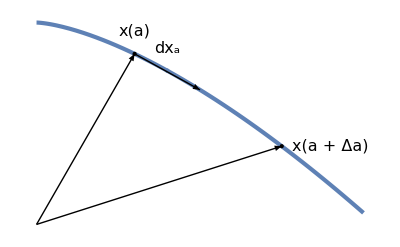

{oneParameterDifferentialFig1.eps,oneParameterDifferentialFig1pn.png}

```mathematica
(*to[start_,end_,ss_:0]=start+(end-start) (1+ss/Norm[end-start]);

setback = {0.4, 0.4} ;*)
o = {0,0};
f = 3 - #^1.5 & ;
pair = {#,f[#]} &;
bold = Style[ #, Bold] &;
fs = 16;
bxOfa = Style[Row[{bold[x],"(a)"}], FontSize-> fs] ;
dxa = Style[Subscript[bold[dx],"a"], FontSize-> fs];
bxOfAplus = Style[Row[{bold[x],"(a + Δa)"}], FontSize-> fs];

p = Plot[
f[x], {x,0,2}, 
PlotTheme->"ThickLines" , 
Axes-> None
] ;
p2 = ListPlot[{
Callout[{0.6,f[0.6]},bxOfa, Above],
Callout[ {1.5, f[1.5]}, bxOfAplus, Right]
},
PlotStyle->Directive[Black,PointSize[Large]]
] ;
p3 = ListPlot[{
Callout[{0.8,f[0.8]},dxa, Above]
},
PlotStyle->PointSize[Tiny]
] ;
g = Show[p,p2, p3, 
Graphics[{
Thick,Arrowheads[0.05],
Arrow[{o,pair[0.6]}],
Arrow[{o,pair[1.5]}],
Arrow[{pair[0.6],pair[1]}]}]
]

peeters`exportForLatex["oneParameterDifferentialFig1", g]
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures" ]
```

/Users/pjoot/project/figures